Phasor Entered Is: 4.33013 + 2.5i In Rectangular Form

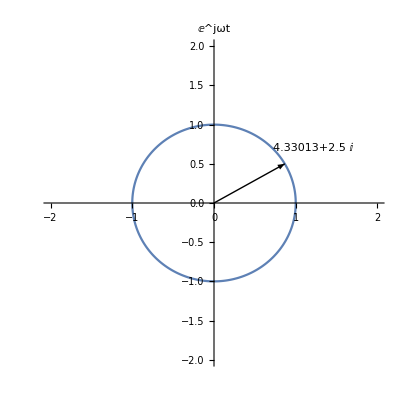

```mathematica
(*This code turns a simple sinusoid input into a rectangular phasor and plots it on the unit circle*)
A= Input["Enter Magnitude: "];
f = Input["Enter Frequency: "];
ϕ1 = π/180*Input["Enter Phase Angle In Degrees"];
flag = Input["Is it sine or cosine? Enter 1 for sine, or 2 for cosine: "];
real=If[flag==1,A*Cos[-π/2+ϕ1],A*Cos[ϕ1]];
imaginary=If[flag==1,ⅉ*A*Sin[-π/2+ϕ1],ⅉ*A*Sin[ϕ1]];
imaginary2=If[flag==1,A*Sin[-π/2+ϕ1],A*Sin[ϕ1]];
phasor = (real + imaginary)//N;
StringTemplate ["Phasor Entered Is: `1` In Rectangular Form"][phasor]
Show[ParametricPlot[{Re[Exp[ⅉ t]],Im[Exp[ⅉ t]]},{t,0,2 π},AspectRatio->1,PlotRange->{{-2,2},{-2,2},PlotStyle->Blue,Thick},PlotLabel->"ⅇ^jωt"],Graphics[Arrow[{{0,0},{real/(√(real^2+imaginary2^2)),imaginary2/(√(real^2+imaginary2^2))}}]],Graphics[Text[phasor,{(1.4*real)/(√(real^2+imaginary2^2)),(1.4*imaginary2)/(√(real^2+imaginary2^2))}]]](*The Arrow represents a unit vector in the direction of the phasor*)
(*The sinusoid entered in this example is 5Cos(0.1t + 30)*)
```

```mathematica
(*This Turns a phasor into a sinusoid. Phaser must be in polar form*)
a= Input["Enter Magnitude: "];
f=Input["Enter The Frequency: "];
ϕ2 = π/180*Input["Enter Phase Angle In Degrees: "];
P[t_] :=a*Exp[ⅉ (2 π f t +ϕ2)];
Animate[Plot[Re[P[t]],{t,0,b},PlotRange->{{0,8 π},{-a-1,a+1}},PlotLabel->StringTemplate["Re{ⅇ^ⅉωt} = Cos(ωt + (`1`)^°)"][ϕ2*180/π]],{b,.01,8 π},AnimationRunning->False]
```

```mathematica
(*This does the same as the previous code, but it can take rectangular form of phasor instead*)
q=Input["Enter Real Part Of Phasor: "];
r=Input["Enter Imaginary Part Of Phasor: "];
ω2=2 π*Input["Enter The Frequency: "];
s=q+ⅉ r;
Mag=Abs[s];
ϕ3 = Arg[s];
StringTemplate["Rectangular Form Of Phasor Entered Is: `1`"][s]
StringTemplate["Polar Form Of Phasor Entered Is: `1`< `2`"][Mag,(ϕ3*180)/π]
F[z_]:=Mag*Exp[ⅉ(ω2 z + ϕ3)];

Animate[Plot[Re[F[z]],{z,0,b},PlotRange->{{0,8 π},{- (Mag)-1,Mag+1}},PlotLabel->StringTemplate["Re{ⅇ^ⅉωt} = Cos(ωt + (`1`)^°)"][ϕ3*180/π]],{b,.01,8π},AnimationRunning->False]
```

Rectangular Form Of Phasor Entered Is: 5 + 5.i

Polar Form Of Phasor Entered Is: 7.07107< 45